```mathematica
Import["C:\\Users\\douwm\\repos\\ca_compression\\functions_to_find_compression_rules.wl"]
```

```mathematica
nRules = numberOfGeneralRules[#]&/@Range[1,6]
```

{256,4294967296,340282366920938463463374607431768211456,13407807929942597099574024998205846127479365820592393377723561443721764030073546976801874298166903427690031858186486050853753882811946569946433649006084096,32317006071311007300714876688669951960444102669715484032130345427524655138867890893197201411522913463688717960921898019494119559150490921095088152386448283120630877367300996091750197750389652106796057638384067568276792218642619756161838094338476170470581645852036305042887575891541065808607552399123930385521914333389668342420684974786564569494856176035326322058077805659331026192708460314150258592864177116725943603718461857357598351152301645904403697613233287231227125684710820209725157101726931323469678542580656697935045997268352998638215525166389437335543602135433229604645318478604952148193555853611059596230656,1090748135619415929462984244733782862448264161996232692431832786189721331849119295216264234525201987223957291796157025273109870820177184063610979765077554799078906298842192989538609825228048205159696851613591638196771886542609324560121290553901886301017900252535799917200010079600026535836800905297805880952350501630195475653911005312364560014847426035293551245843928918752768696279344088055617515694349945406677825140814900616105920256438504578013326493565836047242407382442812245131517757519164899226365743722432277368075027627883045206501792761700945699168497257879683851737049996900961120515655050115561271491492515342105748966629547032786321505730828430221664970324396138635251626409516168005427623435996308921691446181187406395310665404885739434832877428167407495370993511868756359970390117021823616749458620969857006263612082706715408157066575137281027022310927564910276759160520878304632411049364568754920967322982459184763427383790272448438018526977764941072715611580434690827459339991961414242741410599117426060556483763756314527611362658628383368621157993638020878537675545336789915694234433955666315070087213535470255670312004130725495834508357439653828936077080978550578912967907352780054935621561090795845172954115972927479877527738560008204118558930004777748727761853813510493840581861598652211605960308356405941821189714037868726219481498727603653616298856174822413033485438785324024751419417183012281078209729303537372804574372095228703622776363945290869806258422355148507571039619387449629866808188769662815778153079393179093143648340761738581819563002994422790754955061288818308430079648693232179158765918035565216157115402992120276155607873107937477466841528362987708699450152031231862594203085693838944657061346236704234026821102958954951197087076546186622796294536451620756509351018906023773821539532776208676978589731966330308893304665169436185078350641568336944530051437491311298834367265238595404904273455928723949525227184617404367854754610474377019768025576605881038077270707717942221977090385438585844095492116099852538903974655703943973086090930596963360767529964938414598185705963754561497355827813623833288906309004288017321424808663962671333528009232758350873059614118723781422101460198615747386855096896089189180441339558524822867541113212638793675567650340362970031930023397828465318547238244232028015189689660418822976000815437610652254270163595650875433851147123214227266605403581781469090806576468950587661997186505665475715792896}

```mathematica
SetSharedFunction[PSow]; (*Allows you to Sow in parallel*)
PSow[x_]:=Sow[x];
```

```mathematica
testRandomRule[]:=(
dataDimensionality = RandomInteger[{2,6}];
ruleRange = RandomInteger[{1,6}];
ruleNumber = RandomInteger[nRules[[ruleRange]]-1];
startTime = RandomInteger[{1,10}];
res = testRuleRangeDimForReduction[ruleNumber,ruleRange,startTime,dataDimensionality];
If[res >0.01, PSow[{dataDimensionality,ruleRange,startTime,ruleNumber,res}]]
)
```

```mathematica
res = Last@Reap[ParallelDo[testRandomRule[],{10}]]
Save["betterthan046_20210312",res];
```

{{{2,3,8,212018341276542291921501422698475701497,0.25},{6,4,1,10312270764957092634312342376786742142581713355889985853063110312845864451930880993530901424065589447491773835703972455003251423516547361999288310439745202,0.0625},{6,1,9,252,0.015625},{3,6,5,932575150926642860835372819547635507193364635479769185457724603713307181920126503458389951974753376913939910370611012629068441770983015140148074820092919433057741267972932429713270399562765076391183746987963421721006006759726995046731954306597563325727744162319642513291822751431245298471107405117094794443997237346010736599757239362503887032810003802085586426104444424564777505089852190910179276883410223741464376137065616118957405648520896140224929601840350885289481691730419993385081288492012614617620516801392391662722821441743523754457155144145097249306885824661772602752365898563715171531973944620161701393745550631008641602315269600489280319044616247878760390586385159499897600095567766018862732929982925805451732893187545648742600532481283151335054420351239757335742487138415387588689936091473566555261615136505239730066985155263746052891251077771099846401017753960207659099371810215483226056877753455119795955824834487606120857820634806269616019916472072925562585528137808181707072381113128936702877027417562692468547608866719148385535822253113220087536047038877705695117741461589753091518607229866439708919872662846108764598412136232212986309043129170432779621786810854045751994403822251771784432861424750122516126991009544174958862153656828387820649813918305165877506023829324665222651288288488092503622322272546620833554267738468000581339268016394911191057681897579576838464599748386072176359101022718336142609039461275519657846528643991432374619752803851025658940262152362903670389028382260982993151934972069438233798594590839486183469897362224092044122121297531366737031677387065559968860221452554709880251467011904955803865335111762354143902277370043094820397800869450863976588830087439335335621636543846960085957849636263070781606340244174249935545973804390815755073451862526110958688592107732478941629024851410087639256528810146323565446367196845085113971846095336942693894459261127069674411645738867584257562183504951128679852430104362029264666678045378955122326864172850931486697373581227485220259961017988251857485929166948222134633905945934655440823674582719784418177341701022551907710058079797803549314621823567190378095462924837751539960936028323551940796210009873053654584245131294190485177559126859579510746647508942185184487858602063966383576808083342778058567007756105658924830905289056809467612718604143464136526332637703158128300465186038256156013555338539144115082203581876773350875489832975913099910179163809354428047082553356102871979,0.25},{5,5,9,25854373984325408829256834216208326005907948228413617410874406895482409439781079136283133179092790494506154589809572076016566480664716805500420802895534704423146807786409690323695866646353208016903801279388660979685201972332215416380704133411004020631682812737222056985062094324942225155961332958164028035736355243033690680320239737272882153417367111180481621566826739283704017452086601597556816176951113257875226383405342133721651352791720143275389490243009147242520099443039664726426223800355728509415078746203187006962709624185555966690428011409187876993289307641804155677094652986246341220712400149600171703360914,0.15625}}}

```mathematica
testRandomRule[]
```

```mathematica
bt46 = First@Get["betterthan046"];
```

```mathematica
Dimensions[bt46]
```

{241,5}

```mathematica
Count[#,Max[#]]&@bt46[[All,5]]
```

1

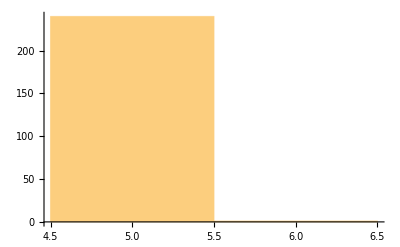
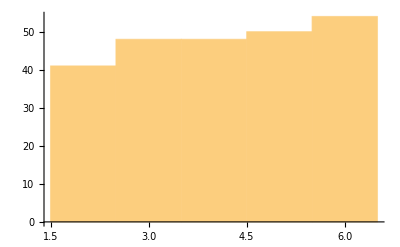
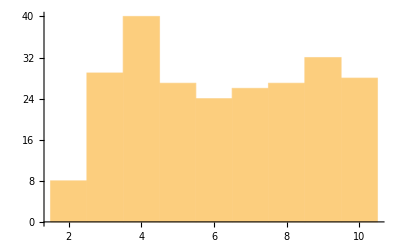
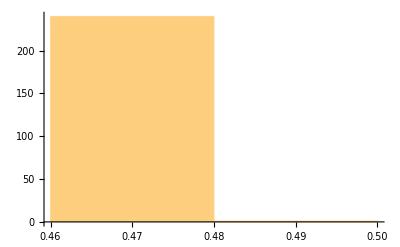

```mathematica
Histogram/@Transpose@bt46[[All,{1,2,3,5}]]
```

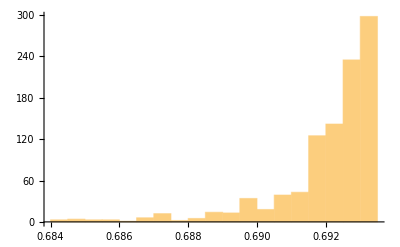

```mathematica
Histogram[Table[Entropy[RandomInteger[{0,1},500]]//N,1000]]
```

```mathematica
Entropy[{0,1,0,0,0}]//N
```

0.500402

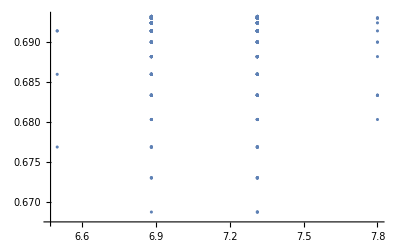

```mathematica
ListPlot[Table[With[{a = RandomInteger[{0,1},100]},
{ByteCount@a/ByteCount@Compress@a,Entropy[a]}],500]]
```

```mathematica
With[{a=RandomInteger[{0,1},4],N[ByteCount[a]/ByteCount[Compress[a]]]]
```